## (a)纯阻性串行电弧故障

-Graphics-

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

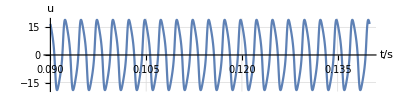

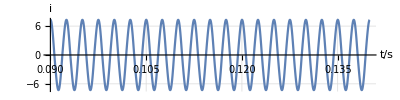

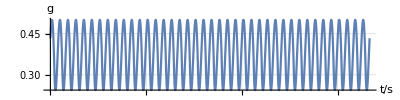

E_arc=

0.537175

融化体积V=

0.200007

U_max=

19.0583

I_max=

8.12766

归一能量e_arc=

0.0034679

-Graphics-

-Graphics-

-Graphics-

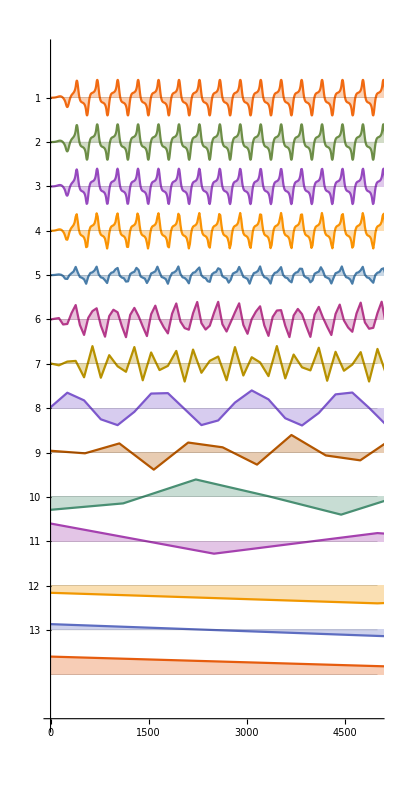

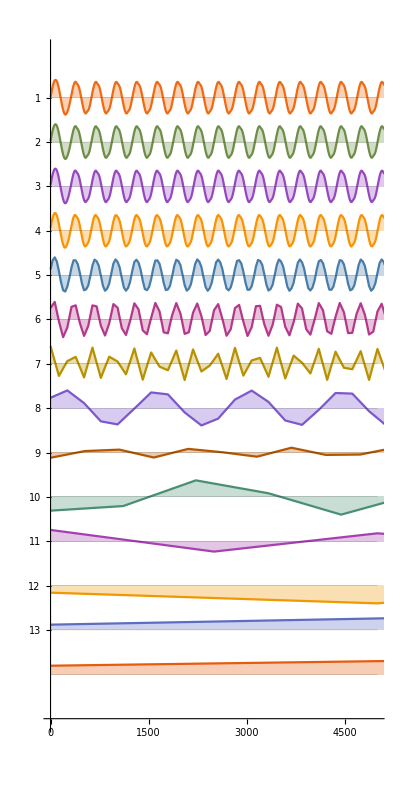

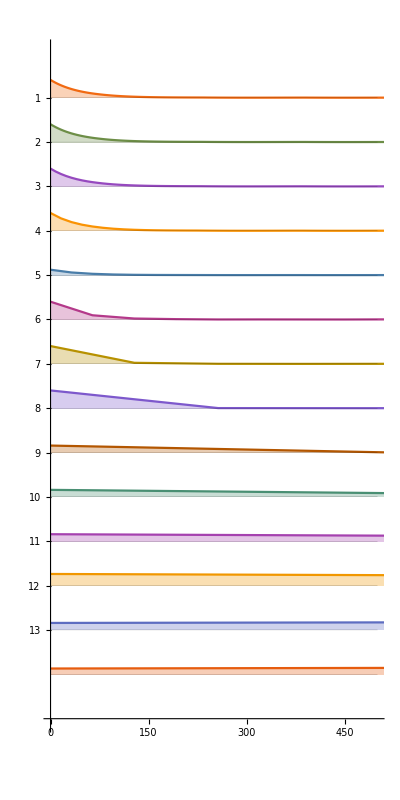

```mathematica
Clear["Global`*"];
R=20;
t1=0.5 10^-3;

θ=t1/(√2);
p0=10;
U=17;
uarc=U/(√2);
ueff=115;
f=400;
result=NDSolve[{u[t]==√2 ueff Cos[2π f t]-R i[t],g[t]u[t]==i[t],g'[t]==g[t]×1/θ((u[t]i[t])/Max[uarc×Abs[i[t]],p0]-1),i[0]==0,g[0]==100,u[0]==ueff},{u,i,g},{t,0,0.2}];
result=result//Flatten;
u=u/.result⟦1⟧;
i=i/.result⟦2⟧;
g=g/.result⟦3⟧;
Plot[u[t],{t,0.09,0.14},AspectRatio->1/4,GridLines->Automatic,GridLinesStyle->Gray,PlotLegends->"电弧电压",AxesLabel->{"t/s","u"}]
Plot[i[t],{t,0.09,0.14},AspectRatio->1/4,GridLines->Automatic,GridLinesStyle->Gray,PlotLegends->"电弧电流",AxesLabel->{"t/s","i"}]
Plot[g[t],{t,0.09,0.14},AspectRatio->1/4,GridLines->Automatic,GridLinesStyle->Gray,PlotLegends->"电弧电导",AxesLabel->{"t/s","g"}]
"E_arc="
Earc=N[∫_0^0.01 u[t]i[t]ⅆt]
"融化体积V="
Earc/(660 904.144+3.98 10^5)×1/(2.7×10^3)10^9
umax=MaxValue[{Abs[u[x]],x>0,x<0.2},x];
imax=MaxValue[{Abs[i[x]],x>0,x<0.2},x];
"\!\(\*SubscriptBox[\(U\), \(max\)]\)="
umax
"\!\(\*SubscriptBox[\(I\), \(max\)]\)="
imax
"\!\(\*SubscriptBox[\(归一能量e\), \(arc\)]\)="
earc=Earc/(umax imax)
n=10000;
ts=Range[n]/n*0.08;
uts=u[ts];
its=i[ts];
gts=g[ts];
"Uts=TimeSeries[uts,{ts}];
Its=TimeSeries[its,{ts}];
Gts=TimeSeries[gts,{ts}];";
Spectrogram[ShortTimeFourier[uts],PlotLegends->"电压频谱图",PlotTheme->"Detailed"]
Spectrogram[ShortTimeFourier[its],PlotLegends->"电流频谱图",PlotTheme->"Detailed"]
Spectrogram[ShortTimeFourier[gts],PlotLegends->"电导频谱图",PlotTheme->"Detailed",PlotRange->{{1,2000},Automatic}]
DiscreteWaveletTransform[uts];
WaveletListPlot[%,AspectRatio->2/1,PlotLegends->"电压小波变换系数图",Ticks->Automatic,PlotLayout->"CommonXAxis",Filling->Axis,PlotTheme->"Scientific",PlotRange->{0,5000}]
DiscreteWaveletTransform[its];
WaveletListPlot[%,AspectRatio->2/1,PlotLegends->"电流小波变换系数图",Ticks->Automatic,PlotLayout->"CommonXAxis",Filling->Axis,PlotTheme->"Scientific",PlotRange->{0,5000}]
DiscreteWaveletTransform[gts];
WaveletListPlot[%,AspectRatio->2/1,PlotLegends->"电导小波变换系数图",Ticks->Automatic,PlotLayout->"CommonXAxis",Filling->Axis,PlotTheme->"Scientific",PlotRange->{0,500}]
```

## (b)组感性串行电弧

-Graphics-

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

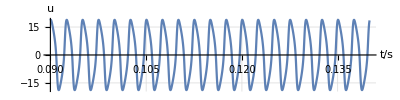

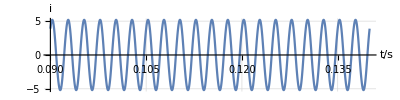

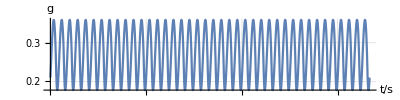

E_arc=

0.371337

融化体积V=

0.13826

U_max=

18.8505

I_max=

5.19072

归一能量e_arc=

0.00379506

-Graphics-

-Graphics-

-Graphics-

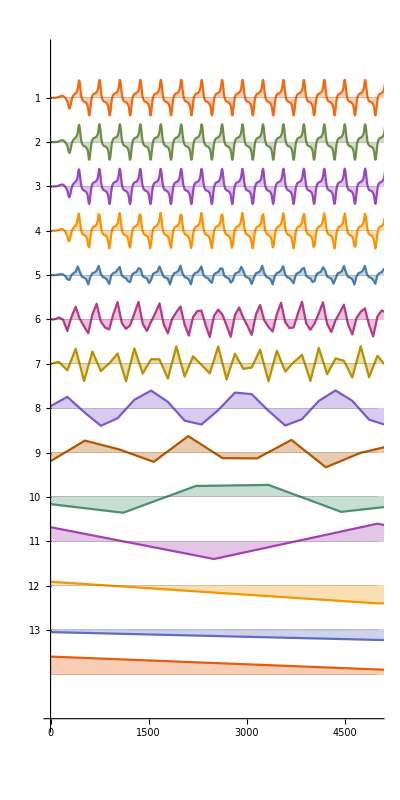

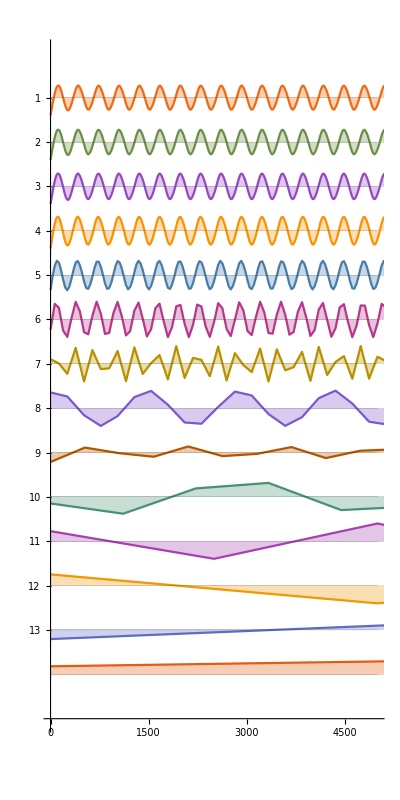

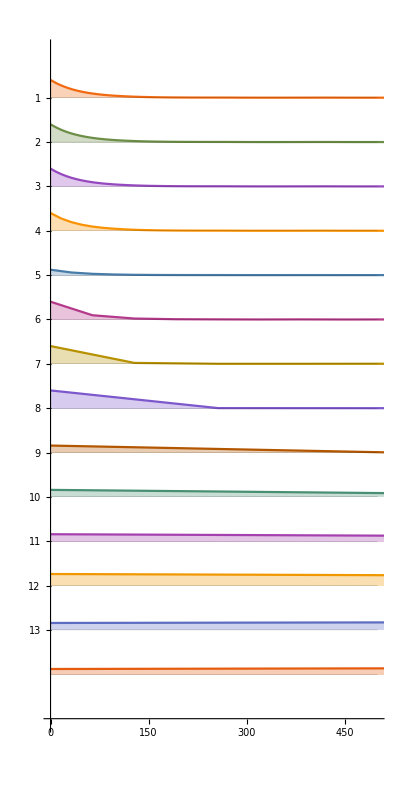

```mathematica
Clear["Global`*"];
R=20;
t1=0.5 10^-3;

θ=t1/(√2);
p0=10;
U=17;
uarc=U/(√2);
ueff=115;
f=400;
L=R/(2π f);
result=NDSolve[{u[t]==√2 ueff Cos[2π f t]-R i[t]-L i'[t],g[t]u[t]==i[t],g'[t]==g[t]×1/θ((u[t]i[t])/Max[uarc×Abs[i[t]],p0]-1),i[0]==0,g[0]==100,u[0]==ueff},{u,i,g},{t,0,0.2}];
result=result//Flatten;
u=u/.result⟦1⟧;
i=i/.result⟦2⟧;
g=g/.result⟦3⟧;
Plot[u[t],{t,0.09,0.14},AspectRatio->1/4,GridLines->Automatic,GridLinesStyle->Gray,PlotLegends->"电弧电压",AxesLabel->{"t/s","u"}]
Plot[i[t],{t,0.09,0.14},AspectRatio->1/4,GridLines->Automatic,GridLinesStyle->Gray,PlotLegends->"电弧电流",AxesLabel->{"t/s","i"}]
Plot[g[t],{t,0.09,0.14},AspectRatio->1/4,GridLines->Automatic,GridLinesStyle->Gray,PlotLegends->"电弧电导",AxesLabel->{"t/s","g"}]
"E_arc="
Earc=N[∫_0^0.01 u[t]i[t]ⅆt]
"融化体积V="
Earc/(660 904.144+3.98 10^5)×1/(2.7×10^3)10^9
umax=MaxValue[{Abs[u[x]],x>0,x<0.2},x];
imax=MaxValue[{Abs[i[x]],x>0,x<0.2},x];
"\!\(\*SubscriptBox[\(U\), \(max\)]\)="
umax
"\!\(\*SubscriptBox[\(I\), \(max\)]\)="
imax
"\!\(\*SubscriptBox[\(归一能量e\), \(arc\)]\)="
earc=Earc/(umax imax)
n=10000;
ts=Range[n]/n*0.08;
uts=u[ts];
its=i[ts];
gts=g[ts];
"Uts=TimeSeries[uts,{ts}];
Its=TimeSeries[its,{ts}];
Gts=TimeSeries[gts,{ts}];";
Spectrogram[ShortTimeFourier[uts],PlotLegends->"电压频谱图",PlotTheme->"Detailed"]
Spectrogram[ShortTimeFourier[its],PlotLegends->"电流频谱图",PlotTheme->"Detailed"]
Spectrogram[ShortTimeFourier[gts],PlotLegends->"电导频谱图",PlotTheme->"Detailed",PlotRange->{{1,2000},Automatic}]
DiscreteWaveletTransform[uts];
WaveletListPlot[%,AspectRatio->2/1,PlotLegends->"电压小波变换系数图",Ticks->Automatic,PlotLayout->"CommonXAxis",Filling->Axis,PlotTheme->"Scientific",PlotRange->{0,5000}]
DiscreteWaveletTransform[its];
WaveletListPlot[%,AspectRatio->2/1,PlotLegends->"电流小波变换系数图",Ticks->Automatic,PlotLayout->"CommonXAxis",Filling->Axis,PlotTheme->"Scientific",PlotRange->{0,5000}]
DiscreteWaveletTransform[gts];
WaveletListPlot[%,AspectRatio->2/1,PlotLegends->"电导小波变换系数图",Ticks->Automatic,PlotLayout->"CommonXAxis",Filling->Axis,PlotTheme->"Scientific",PlotRange->{0,500}]
```

## (c)阻容性串行电弧

-Graphics-

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

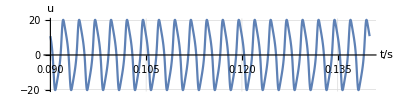

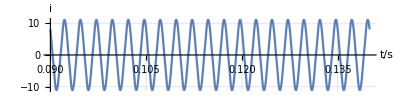

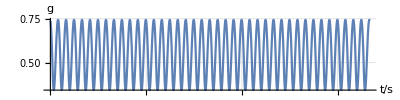

E_arc=

1.05698

融化体积V=

0.393546

U_max=

59.5443

I_max=

11.0515

归一能量e_arc=

0.00160622

-Graphics-

-Graphics-

-Graphics-

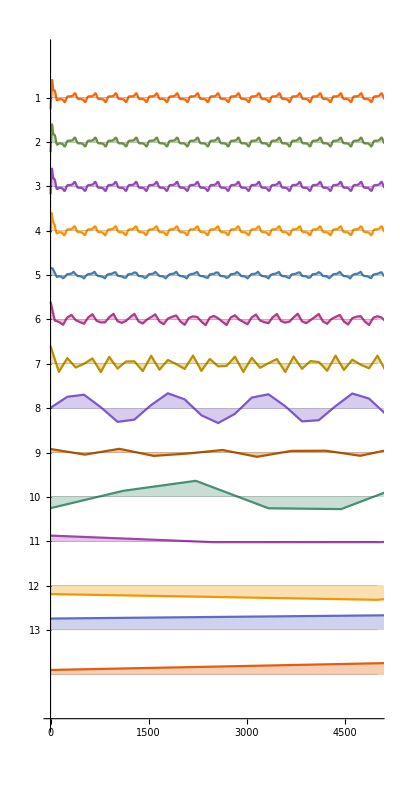

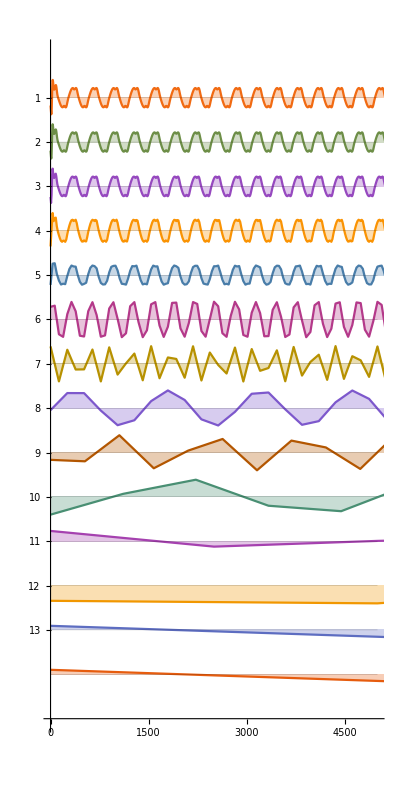

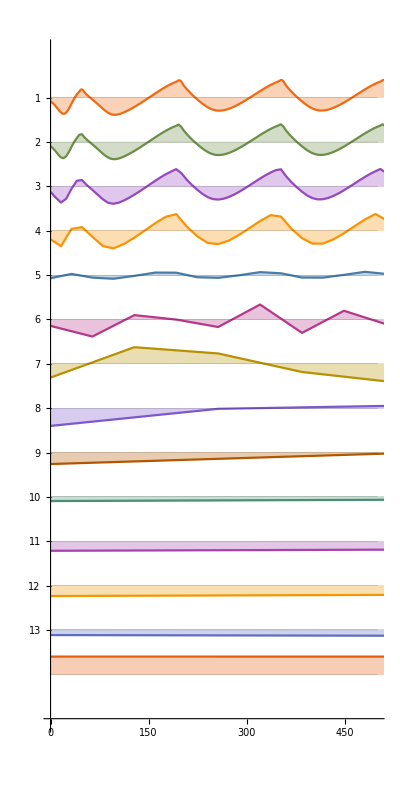

```mathematica
Clear["Global`*"];
R=20;
t1=0.5 10^-3;

θ=t1/(√2);
p0=10;
U=17;
uarc=U/(√2);
ueff=115;
f=400;
c=1/(2π f R);
result=NDSolve[{u[t]==√2 ueff Cos[2π f t]-uc[t],g[t]u[t]==i[t],g'[t]==g[t]×1/θ((u[t]i[t])/Max[uarc×Abs[i[t]],p0]-1),i[t]==uc[t]/R+c uc'[t],i[0]==0,g[0]==100,u[0]==ueff},{u,i,g,uc},{t,0,0.2}];
result=result//Flatten;
u=u/.result⟦1⟧;
i=i/.result⟦2⟧;
g=g/.result⟦3⟧;
Plot[u[t],{t,0.09,0.14},AspectRatio->1/4,GridLines->Automatic,GridLinesStyle->Gray,PlotLegends->"电弧电压",AxesLabel->{"t/s","u"}]
Plot[i[t],{t,0.09,0.14},AspectRatio->1/4,GridLines->Automatic,GridLinesStyle->Gray,PlotLegends->"电弧电流",AxesLabel->{"t/s","i"}]
Plot[g[t],{t,0.09,0.14},AspectRatio->1/4,GridLines->Automatic,GridLinesStyle->Gray,PlotLegends->"电弧电导",AxesLabel->{"t/s","g"}]
"E_arc="
Earc=N[∫_0^0.01 u[t]i[t]ⅆt]
"融化体积V="
Earc/(660 904.144+3.98 10^5)×1/(2.7×10^3)10^9
umax=MaxValue[{Abs[u[x]],x>0,x<0.2},x];
imax=MaxValue[{Abs[i[x]],x>0,x<0.2},x];
"\!\(\*SubscriptBox[\(U\), \(max\)]\)="
umax
"\!\(\*SubscriptBox[\(I\), \(max\)]\)="
imax
"\!\(\*SubscriptBox[\(归一能量e\), \(arc\)]\)="
earc=Earc/(umax imax)
n=10000;
ts=Range[n]/n*0.08;
uts=u[ts];
its=i[ts];
gts=g[ts];
"Uts=TimeSeries[uts,{ts}];
Its=TimeSeries[its,{ts}];
Gts=TimeSeries[gts,{ts}];";
Spectrogram[ShortTimeFourier[uts],PlotLegends->"电压频谱图",PlotTheme->"Detailed"]
Spectrogram[ShortTimeFourier[its],PlotLegends->"电流频谱图",PlotTheme->"Detailed"]
Spectrogram[ShortTimeFourier[gts],PlotLegends->"电导频谱图",PlotTheme->"Detailed",PlotRange->{{1,2000},Automatic}]
DiscreteWaveletTransform[uts];
WaveletListPlot[%,AspectRatio->2/1,PlotLegends->"电压小波变换系数图",Ticks->Automatic,PlotLayout->"CommonXAxis",Filling->Axis,PlotTheme->"Scientific",PlotRange->{0,5000}]
DiscreteWaveletTransform[its];
WaveletListPlot[%,AspectRatio->2/1,PlotLegends->"电流小波变换系数图",Ticks->Automatic,PlotLayout->"CommonXAxis",Filling->Axis,PlotTheme->"Scientific",PlotRange->{0,5000}]
DiscreteWaveletTransform[gts];
WaveletListPlot[%,AspectRatio->2/1,PlotLegends->"电导小波变换系数图",Ticks->Automatic,PlotLayout->"CommonXAxis",Filling->Axis,PlotTheme->"Scientific",PlotRange->{0,500}]
```

## (d)纯阻性并行电弧

-Graphics-

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

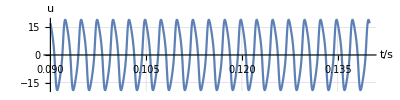

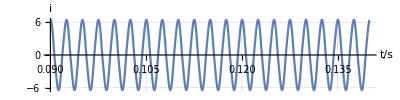

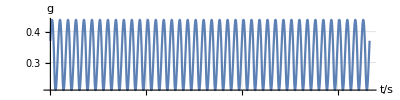

E_arc=

0.469285

融化体积V=

0.174729

U_max=

19.1149

I_max=

8.1236

归一能量e_arc=

0.00302214

-Graphics-

-Graphics-

-Graphics-

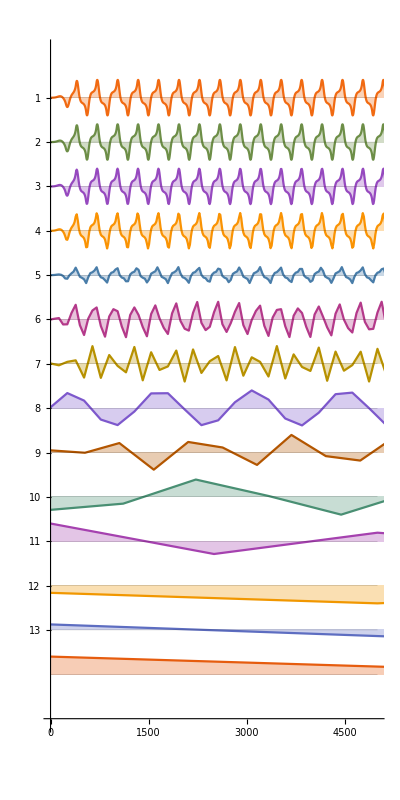

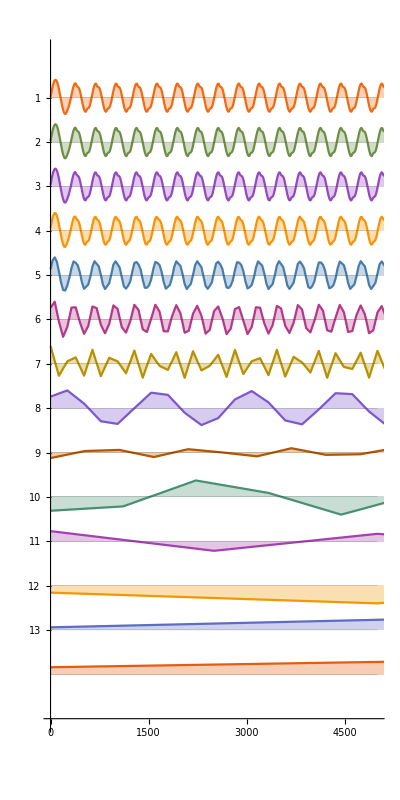

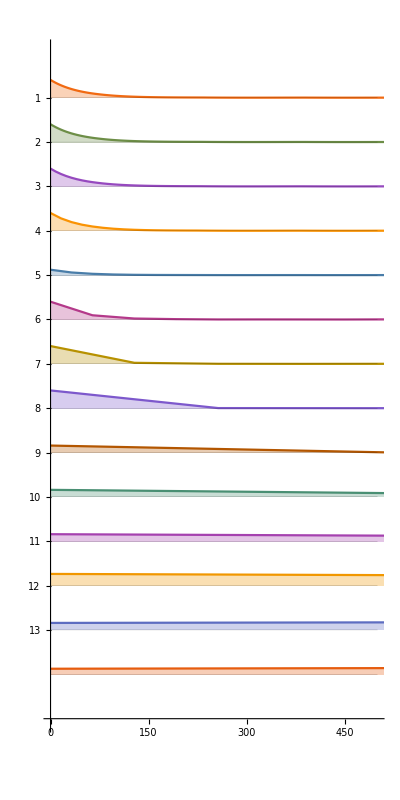

```mathematica
Clear["Global`*"];
R=20;
t1=0.5 10^-3;

θ=t1/(√2);
p0=10;
U=17;
uarc=U/(√2);
ueff=115;
f=400;
result=NDSolve[{u[t]==√2 ueff Cos[2π f t]-R (i[t]+u[t]/R),g[t]u[t]==i[t],g'[t]==g[t]×1/θ((u[t]i[t])/Max[uarc×Abs[i[t]],p0]-1),i[0]==0,g[0]==100,u[0]==ueff},{u,i,g},{t,0,0.2}];
result=result//Flatten;
u=u/.result⟦1⟧;
i=i/.result⟦2⟧;
g=g/.result⟦3⟧;
Plot[u[t],{t,0.09,0.14},AspectRatio->1/4,GridLines->Automatic,GridLinesStyle->Gray,PlotLegends->"电弧电压",AxesLabel->{"t/s","u"}]
Plot[i[t],{t,0.09,0.14},AspectRatio->1/4,GridLines->Automatic,GridLinesStyle->Gray,PlotLegends->"电弧电流",AxesLabel->{"t/s","i"}]
Plot[g[t],{t,0.09,0.14},AspectRatio->1/4,GridLines->Automatic,GridLinesStyle->Gray,PlotLegends->"电弧电导",AxesLabel->{"t/s","g"}]
"E_arc="
Earc=N[∫_0^0.01 u[t]i[t]ⅆt]
"融化体积V="
Earc/(660 904.144+3.98 10^5)×1/(2.7×10^3)10^9
umax=MaxValue[{Abs[u[x]],x>0,x<0.2},x];
imax=MaxValue[{Abs[i[x]],x>0,x<0.2},x];
"\!\(\*SubscriptBox[\(U\), \(max\)]\)="
umax
"\!\(\*SubscriptBox[\(I\), \(max\)]\)="
imax
"\!\(\*SubscriptBox[\(归一能量e\), \(arc\)]\)="
earc=Earc/(umax imax)
n=10000;
ts=Range[n]/n*0.08;
uts=u[ts];
its=i[ts];
gts=g[ts];
"Uts=TimeSeries[uts,{ts}];
Its=TimeSeries[its,{ts}];
Gts=TimeSeries[gts,{ts}];";
Spectrogram[ShortTimeFourier[uts],PlotLegends->"电压频谱图",PlotTheme->"Detailed"]
Spectrogram[ShortTimeFourier[its],PlotLegends->"电流频谱图",PlotTheme->"Detailed"]
Spectrogram[ShortTimeFourier[gts],PlotLegends->"电导频谱图",PlotTheme->"Detailed",PlotRange->{{1,2000},Automatic}]
DiscreteWaveletTransform[uts];
WaveletListPlot[%,AspectRatio->2/1,PlotLegends->"电压小波变换系数图",Ticks->Automatic,PlotLayout->"CommonXAxis",Filling->Axis,PlotTheme->"Scientific",PlotRange->{0,5000}]
DiscreteWaveletTransform[its];
WaveletListPlot[%,AspectRatio->2/1,PlotLegends->"电流小波变换系数图",Ticks->Automatic,PlotLayout->"CommonXAxis",Filling->Axis,PlotTheme->"Scientific",PlotRange->{0,5000}]
DiscreteWaveletTransform[gts];
WaveletListPlot[%,AspectRatio->2/1,PlotLegends->"电导小波变换系数图",Ticks->Automatic,PlotLayout->"CommonXAxis",Filling->Axis,PlotTheme->"Scientific",PlotRange->{0,500}]
```

## (e)组感性并行电弧

-Graphics-

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

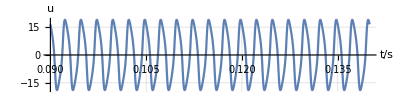

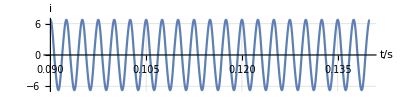

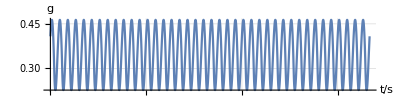

E_arc=

0.62023

融化体积V=

0.230931

U_max=

50.948

I_max=

6.74651

归一能量e_arc=

0.00180446

-Graphics-

-Graphics-

-Graphics-

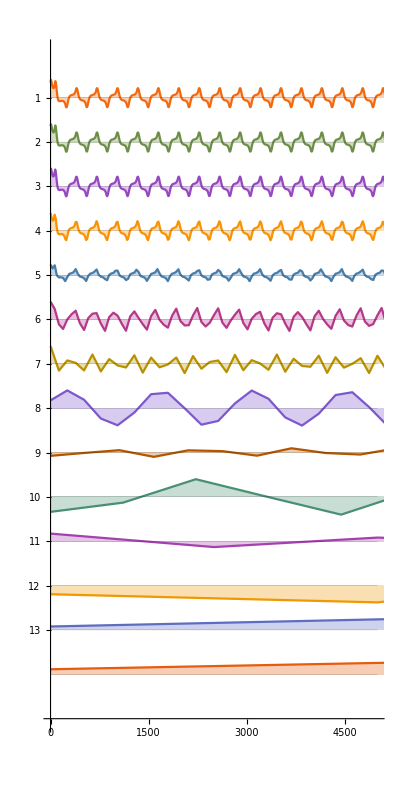

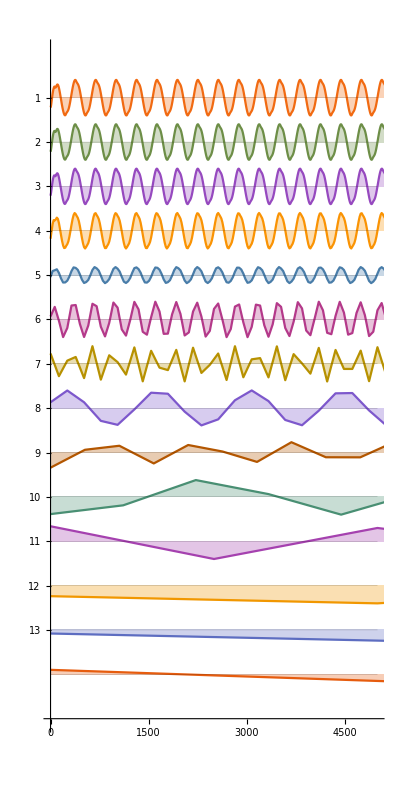

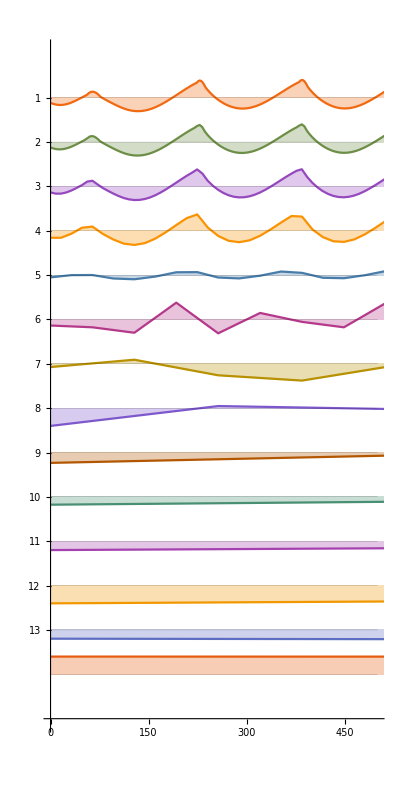

```mathematica
Clear["Global`*"];
R=20;
t1=0.5 10^-3;

θ=t1/(√2);
p0=10;
U=17;
uarc=U/(√2);
ueff=115;
f=400;
L=R/(2π f);
result=NDSolve[{u[t]==√2 ueff Cos[2π f t]-R (i2[t]+i[t]),u[t]==R i2[t]+L i2'[t],g[t]u[t]==i[t],g'[t]==g[t]×1/θ((u[t]i[t])/Max[uarc×Abs[i[t]],p0]-1),i[0]==0,g[0]==100,u[0]==ueff},{u,i,g,i2},{t,0,0.2}];
result=result//Flatten;
u=u/.result⟦1⟧;
i=i/.result⟦2⟧;
g=g/.result⟦3⟧;
Plot[u[t],{t,0.09,0.14},AspectRatio->1/4,GridLines->Automatic,GridLinesStyle->Gray,PlotLegends->"电弧电压",AxesLabel->{"t/s","u"}]
Plot[i[t],{t,0.09,0.14},AspectRatio->1/4,GridLines->Automatic,GridLinesStyle->Gray,PlotLegends->"电弧电流",AxesLabel->{"t/s","i"}]
Plot[g[t],{t,0.09,0.14},AspectRatio->1/4,GridLines->Automatic,GridLinesStyle->Gray,PlotLegends->"电弧电导",AxesLabel->{"t/s","g"}]
"E_arc="
Earc=N[∫_0^0.01 u[t]i[t]ⅆt]
"融化体积V="
Earc/(660 904.144+3.98 10^5)×1/(2.7×10^3)10^9
umax=MaxValue[{Abs[u[x]],x>0,x<0.2},x];
imax=MaxValue[{Abs[i[x]],x>0,x<0.2},x];
"\!\(\*SubscriptBox[\(U\), \(max\)]\)="
umax
"\!\(\*SubscriptBox[\(I\), \(max\)]\)="
imax
"\!\(\*SubscriptBox[\(归一能量e\), \(arc\)]\)="
earc=Earc/(umax imax)
n=10000;
ts=Range[n]/n*0.08;
uts=u[ts];
its=i[ts];
gts=g[ts];
"Uts=TimeSeries[uts,{ts}];
Its=TimeSeries[its,{ts}];
Gts=TimeSeries[gts,{ts}];";
Spectrogram[ShortTimeFourier[uts],PlotLegends->"电压频谱图",PlotTheme->"Detailed"]
Spectrogram[ShortTimeFourier[its],PlotLegends->"电流频谱图",PlotTheme->"Detailed"]
Spectrogram[ShortTimeFourier[gts],PlotLegends->"电导频谱图",PlotTheme->"Detailed",PlotRange->{{1,2000},Automatic}]
DiscreteWaveletTransform[uts];
WaveletListPlot[%,AspectRatio->2/1,PlotLegends->"电压小波变换系数图",Ticks->Automatic,PlotLayout->"CommonXAxis",Filling->Axis,PlotTheme->"Scientific",PlotRange->{0,5000}]
DiscreteWaveletTransform[its];
WaveletListPlot[%,AspectRatio->2/1,PlotLegends->"电流小波变换系数图",Ticks->Automatic,PlotLayout->"CommonXAxis",Filling->Axis,PlotTheme->"Scientific",PlotRange->{0,5000}]
DiscreteWaveletTransform[gts];
WaveletListPlot[%,AspectRatio->2/1,PlotLegends->"电导小波变换系数图",Ticks->Automatic,PlotLayout->"CommonXAxis",Filling->Axis,PlotTheme->"Scientific",PlotRange->{0,500}]
```

## (f)阻容性并行电弧

-Graphics-

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

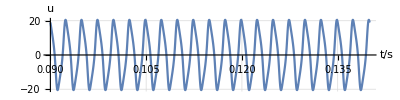

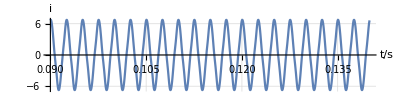

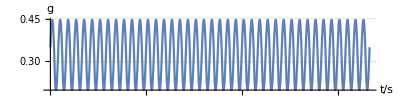

E_arc=

0.628088

融化体积V=

0.233857

U_max=

53.8569

I_max=

6.74767

归一能量e_arc=

0.00172832

-Graphics-

-Graphics-

-Graphics-

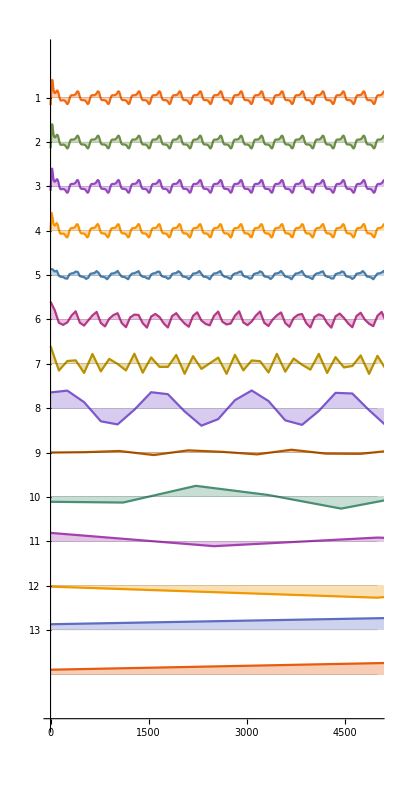

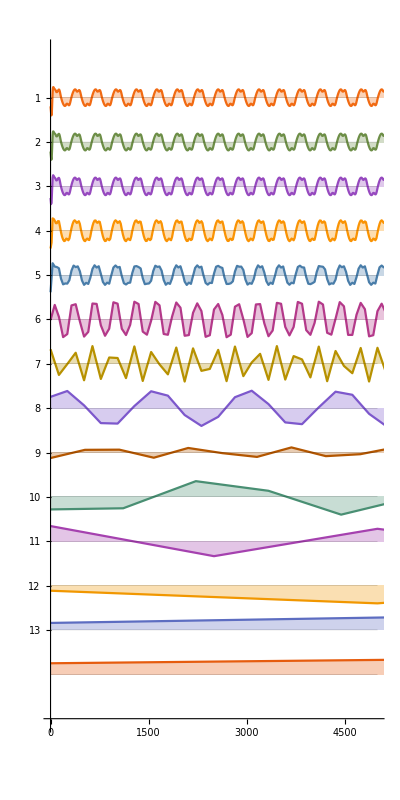

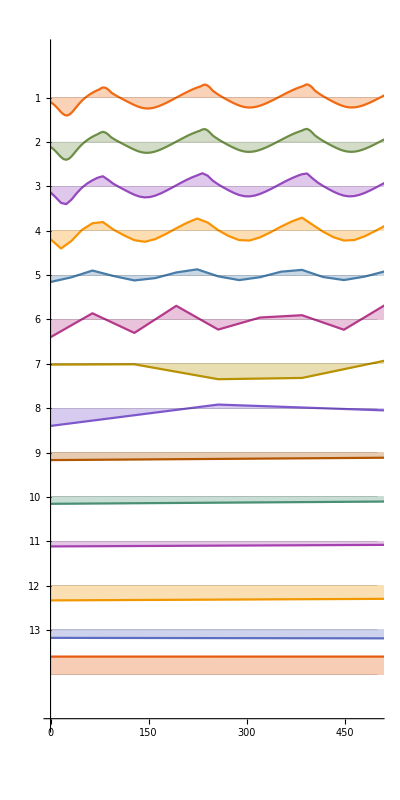

```mathematica
Clear["Global`*"];
R=20;
t1=0.5 10^-3;

θ=t1/(√2);
p0=10;
U=17;
uarc=U/(√2);
ueff=115;
f=400;
c=1/(2π f R);
result=NDSolve[{u[t]==√2 ueff Cos[2π f t]-R (i2[t]+i[t]+c u'[t]),u[t]==R i2[t],g[t]u[t]==i[t],g'[t]==g[t]×1/θ((u[t]i[t])/Max[uarc×Abs[i[t]],p0]-1),i[0]==0,g[0]==100,u[0]==ueff},{u,i,g,i2},{t,0,0.2}];
result=result//Flatten;
u=u/.result⟦1⟧;
i=i/.result⟦2⟧;
g=g/.result⟦3⟧;
Plot[u[t],{t,0.09,0.14},AspectRatio->1/4,GridLines->Automatic,GridLinesStyle->Gray,PlotLegends->"电弧电压",AxesLabel->{"t/s","u"}]
Plot[i[t],{t,0.09,0.14},AspectRatio->1/4,GridLines->Automatic,GridLinesStyle->Gray,PlotLegends->"电弧电流",AxesLabel->{"t/s","i"}]
Plot[g[t],{t,0.09,0.14},AspectRatio->1/4,GridLines->Automatic,GridLinesStyle->Gray,PlotLegends->"电弧电导",AxesLabel->{"t/s","g"}]
"E_arc="
Earc=N[∫_0^0.01 u[t]i[t]ⅆt]
"融化体积V="
Earc/(660 904.144+3.98 10^5)×1/(2.7×10^3)10^9
umax=MaxValue[{Abs[u[x]],x>0,x<0.2},x];
imax=MaxValue[{Abs[i[x]],x>0,x<0.2},x];
"\!\(\*SubscriptBox[\(U\), \(max\)]\)="
umax
"\!\(\*SubscriptBox[\(I\), \(max\)]\)="
imax
"\!\(\*SubscriptBox[\(归一能量e\), \(arc\)]\)="
earc=Earc/(umax imax)
n=10000;
ts=Range[n]/n*0.08;
uts=u[ts];
its=i[ts];
gts=g[ts];
"Uts=TimeSeries[uts,{ts}];
Its=TimeSeries[its,{ts}];
Gts=TimeSeries[gts,{ts}];";
Spectrogram[ShortTimeFourier[uts],PlotLegends->"电压频谱图",PlotTheme->"Detailed"]
Spectrogram[ShortTimeFourier[its],PlotLegends->"电流频谱图",PlotTheme->"Detailed"]
Spectrogram[ShortTimeFourier[gts],PlotLegends->"电导频谱图",PlotTheme->"Detailed",PlotRange->{{1,2000},Automatic}]
DiscreteWaveletTransform[uts];
WaveletListPlot[%,AspectRatio->2/1,PlotLegends->"电压小波变换系数图",Ticks->Automatic,PlotLayout->"CommonXAxis",Filling->Axis,PlotTheme->"Scientific",PlotRange->{0,5000}]
DiscreteWaveletTransform[its];
WaveletListPlot[%,AspectRatio->2/1,PlotLegends->"电流小波变换系数图",Ticks->Automatic,PlotLayout->"CommonXAxis",Filling->Axis,PlotTheme->"Scientific",PlotRange->{0,5000}]
DiscreteWaveletTransform[gts];
WaveletListPlot[%,AspectRatio->2/1,PlotLegends->"电导小波变换系数图",Ticks->Automatic,PlotLayout->"CommonXAxis",Filling->Axis,PlotTheme->"Scientific",PlotRange->{0,500}]
```